{0.,0.}

{1,√3}

{-1,√3}

{1,-√3}

{-1,-√3}

{0.,1.}

{(√3)/2,0.5}

{-(√3)/2,0.5}

{EdgeForm[Directive[Thickness[Large],-Graphics-]],-Graphics-,Triangle[{{0.,0.},{1,√3},{-1,√3}}],-Graphics-,Triangle[{{0.,0.},{1,-√3},{-1,-√3}}]}

{Thickness[Large],-Graphics-,Arrow[{{0.,-0.5},{0.,0.5}}],Arrow[{{1.43301,1.98205},{0.566987,1.48205}}],Arrow[{{-1.43301,1.98205},{-0.566987,1.48205}}],Arrow[{{0.566987,-1.48205},{1.43301,-1.98205}}],Arrow[{{-0.566987,-1.48205},{-1.43301,-1.98205}}]}

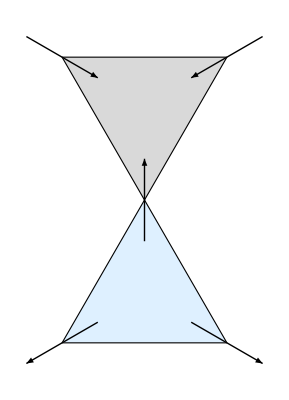

```mathematica
P0={0.,0.}
P1={1,Sqrt[3]}
P2={-1,Sqrt[3]}
P3={1,-Sqrt[3]}
P4={-1,-Sqrt[3]}
Vert={0.,1.}
Cant1={Sqrt[3]/2,0.5}
Cant2={-Sqrt[3]/2,0.5}
ListOne={EdgeForm[Directive[Thick,Black]],LightGray,Triangle[{P0,P1,P2}],LightBlue,Triangle[{P0,P3,P4}]}
ListTwo={Thick,Black,Arrow[{P0-0.5Vert,P0+0.5Vert}],Arrow[{P1+0.5Cant1,P1-0.5Cant1}],Arrow[{P2+0.5Cant2,P2-0.5Cant2}],Arrow[{P3+0.5Cant2,P3-0.5Cant2}],Arrow[{P4+0.5Cant1,P4-0.5Cant1}]}
Graphics[Join[ListOne,ListTwo]]
```

```mathematica
Eigenvalues[I*{{0,-B1,0,-J},{B1,0,J,0},{0,-J,0,-B2},{J,0,B2,0}}]
```

{1/2 (-B1-B2-√(B1^2-2 B1 B2+B2^2+4 J^2)),1/2 (B1+B2-√(B1^2-2 B1 B2+B2^2+4 J^2)),1/2 (-B1-B2+√(B1^2-2 B1 B2+B2^2+4 J^2)),1/2 (B1+B2+√(B1^2-2 B1 B2+B2^2+4 J^2))}

```mathematica
Eigenvalues[{{0,-B1},{B1,0}}]
```

{ⅈ B1,-ⅈ B1}

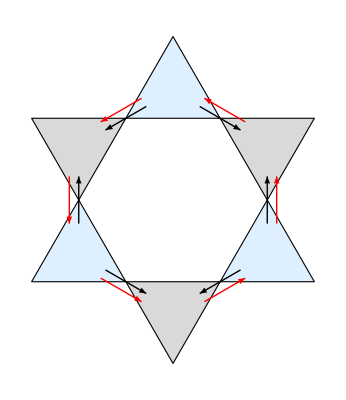

```mathematica
P0={0.,0.};
P1={1,Sqrt[3]};
P2={-1,Sqrt[3]};
P3={1,-Sqrt[3]};
P4={-1,-Sqrt[3]};
P5=2*P1;
P6=P1+{2,0};
P7=P1+{4,0};
P8=P6+P3;
P9=P3+{4,0};
P10=P4+{4,0};
P11=2*P3;

Vert={0.,1.};
Cant1={Sqrt[3]/2,0.5};
Cant2={-Sqrt[3]/2,0.5};

ListOne={EdgeForm[Directive[Thick,Black]],LightGray,Triangle[{P0,P1,P2}],Triangle[{P6,P7,P8}],Triangle[{P3,P11,P10}],LightBlue,Triangle[{P0,P3,P4}],Triangle[{P1,P5,P6}],Triangle[{P8,P9,P10}]};

ListTwo={Thick,Black,Arrow[{P0-0.5Vert,P0+0.5Vert}],Arrow[{P1+0.5Cant1,P1-0.5Cant1}],Arrow[{P8-0.5Vert,P8+0.5Vert}],Arrow[{P3+0.5Cant2,P3-0.5Cant2}],Arrow[{P10+0.5Cant1,P10-0.5Cant1}],Arrow[{P6+0.5Cant2,P6-0.5Cant2}]};

ShiftDistance=0.2;

Shift1={1,0}*ShiftDistance;
Shift2={0.5,0.5*Sqrt[3]}*ShiftDistance;
Shift3={-0.5,0.5*Sqrt[3]}*ShiftDistance;

ListThree={Red,Arrow[{P0-Shift1+0.5Vert,P0-Shift1-0.5Vert}],Arrow[{P1+Shift3+0.5Cant1,P1+Shift3-0.5Cant1}],Arrow[{P8+Shift1-0.5Vert,P8+Shift1+0.5Vert}],Arrow[{P3-Shift2+0.5Cant2,P3-Shift2-0.5Cant2}],Arrow[{P10-Shift3-0.5Cant1,P10-Shift3+0.5Cant1}],Arrow[{P6+Shift2-0.5Cant2,P6+Shift2+0.5Cant2}]};

Graphics[Join[ListOne,ListTwo,ListThree]]
```

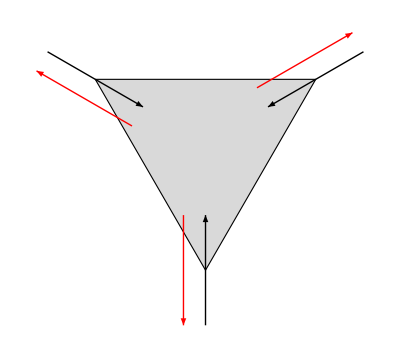

```mathematica
P0={0.,0.};
P1={1,Sqrt[3]};
P2={-1,Sqrt[3]};

Vert={0.,1.};
Cant1={Sqrt[3]/2,0.5};
Cant2={-Sqrt[3]/2,0.5};

ListOne={EdgeForm[Directive[Thick,Black]],LightGray,Triangle[{P0,P1,P2}]};

ListTwo={Thick,Black,Arrow[{P0-0.5Vert,P0+0.5Vert}],Arrow[{P1+0.5Cant1,P1-0.5Cant1}],Arrow[{P2+0.5Cant2,P2-0.5Cant2}]};

ShiftDistance=0.2;

Shift1={1,0}*ShiftDistance;
Shift2={0.5,0.5*Sqrt[3]}*ShiftDistance;
Shift3={-0.5,0.5*Sqrt[3]}*ShiftDistance;

ListThree={Red,Arrow[{P0-Shift1+0.5Vert,P0-Shift1-0.5Vert}],Arrow[{P1+Shift3-0.5Cant1,P1+Shift3+0.5Cant1}],Arrow[{P2-Shift2-0.5Cant2,P2-Shift2+0.5Cant2}]};

Graphics[Join[ListOne,ListTwo,ListThree]]
```